```mathematica
data=Import["https://finance.yahoo.com/quote/GOOG/history?p=GOOG","Data"];
dates=DateList[#]&/@data[[3,2,All,1]];
prices=Interpreter["Number"][#]&/@data[[3,2,All,2]];
```

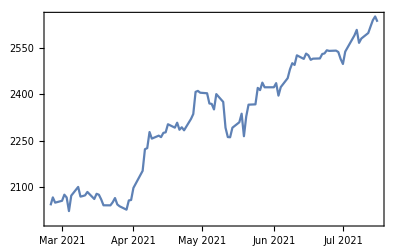

```mathematica
DateListPlot[Transpose[{dates,prices}]]
```